### Sigmoid Function Overview
The sigmoid function is a key function in the field of machine learning, especially in the context of logistic regression and neural networks for binary classification. It maps any real number to the (0, 1) interval, making it suitable for probability representation and binary outcomes.

```mathematica
TraditionalForm[HoldForm[Sigmoid[x]==1/(1+E^-x)]]
```

Sigmoid(x)==1/(1+ⅇ^-x)

- **Significance of the Sigmoid Function** The sigmoid function is particularly interesting due to its ability to model an “S”-shaped curve, providing a natural threshold phenomenon. This is essential in binary decisions, like Yes/No outcomes in binary classification tasks.

- **Domain and Codomain:**
  - **Domain:** (all real numbers)
  - **Codomain:** (0, 1), which is ideal for representing probabilities.
  
- **Properties:**
  - **Injective:** Each input gives a unique output, so it’s one-to-one.
  - **Surjective:** Not onto if we consider the codomain to be [0, 1], as it does not reach exactly 0 or 1, but approaches them asymptotically. But it is surjective if the codomain is considered as (0, 1).
  - **Bijective:** Not bijective, as it is not surjective if codomain is  [0, 1].
  
- **Composition with Other Functions:**
  - Commonly composed with the log loss function to compute cross-entropy loss in logistic regression. This helps in evaluating the probability outputs against actual binary labels in training data.

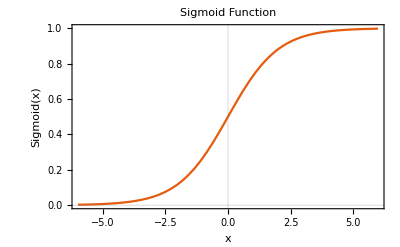

```mathematica
(*Define the sigmoid function*)sigmoid[x_]:=1/(1+Exp[-x])

(*Plot the function*)
Plot[sigmoid[x],{x,-6,6},PlotRange->{0,1},AxesLabel->{"x","Sigmoid(x)"},PlotLabel->"Sigmoid Function",PlotTheme->"Scientific"]
```

### Discussion and Analysis
The sigmoid function’s smooth and continuous nature makes it indispensable in scenarios where we need to smoothly transition from one state to another, based on the input’s magnitude. Its derivative, which is non-zero everywhere, is useful in gradient-based optimization methods, as it ensures that there are always gradients available to drive the adjustments during model training.

```mathematica
TraditionalForm[HoldForm[Sigmoid[x,k,x0]==1/(1+E^(-k*(x-x0)))]]
```

Sigmoid(x,k,x0)==1/(1+ⅇ^(-k (x-x0)))

```mathematica
Manipulate[Plot[1/(1+Exp[-k*(x-x0)]),{x,-10,10},PlotRange->{0,1},AxesLabel->{"x","Sigmoid(x)"},PlotLabel->"Interactive Sigmoid Function",PlotTheme->"Scientific"],{{k,1,"Steepness"},0.5,5,0.1},{{x0,0,"Midpoint"},-5,5,0.1}] (*Interactive visualization of the sigmoid function*)
```